```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 7/ohg6-hw7/";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";*)

SetDirectory[main];
$Line=0;
```

FittedModel[3.61155+0.384644 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3.61155 | 0.161218 | 22.4017 | 1.34836×10^-14
x | 0.384644 | 0.137165 | 2.80423 | 0.0117298

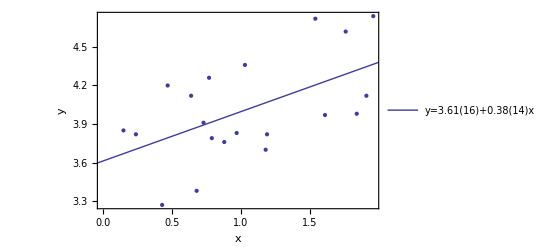

1/leastsquares.png

```mathematica
data=Import["1/data1.txt","Data"];
weights=Table[2,{i,Length[data]}];
model=LinearModelFit[data,x,x,Weights->weights]
model["ParameterTable"]
Show[ListPlot[data,PlotTheme->"Classic"],Plot[model[x],{x,-1,3},PlotTheme->"Classic",PlotLegends->Placed[{"y=3.61(16)+0.38(14)x"},{Right,0.2}]],Frame->True,FrameTicks->{{True,None},{True,None}},FrameLabel->{"x","y"}]
Export["1/leastsquares.png",%]
```

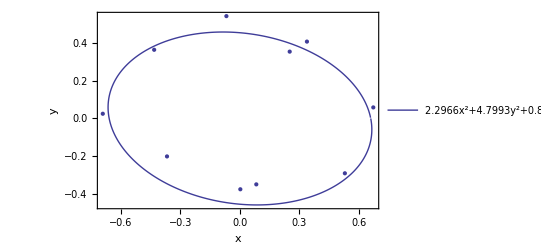

2/ellipse.png

```mathematica
data=Import["2/data2.txt","Data"];
Show[ListPlot[data,PlotTheme->"Classic"],ListLinePlot[Import["2/dataout.txt","Data"],PlotTheme->"Classic",PlotLegends->Placed[{"2.2966x^2+4.7993y^2+0.8553xy = 1"},{Center,Center}]],PlotRange->All,Axes->False,Frame->True,FrameTicks->{{True,None},{True,None}},FrameLabel->{"x","y"}]
Export["2/ellipse.png",%]
```